```mathematica
(*initial parameters*)
kdteto1=1;
kd1=20;
prob1=1;
kdb1=20;
teto1=2;
v1=1;
```

```mathematica
(*defining enrichment*)
fteto[db_,kdteto_,v_]:=db/v/(kdteto+db/v)
fnsb[db_,kd_,v_]:=db/v/(kd+db/v)
fns[df_,kd_,v_]:=df/v/(kd+df/v)
b[db_,df_,kd_,kdteto_,kdb_,v_]:=(fteto[db,kdteto,v]-fnsb[db,kdb,v])/fns[df,kd,v]
a[db_,df_,kd_,kdb_,v_]:=(fnsb[db,kdb,v]-fns[df,kd,v])/fns[df,kd,v]

conc[df_,kdteto_,cteto_,v_]:=Piecewise[{{df-(fteto[df,kdteto,v] cteto),df-(fteto[df,kdteto,v] cteto)>=0},{0,df-(fteto[df,kdteto,v] cteto)<0}}]

Enr[df_,kd_,kdteto_,kdb_,cteto_,prob_,v_]:=b[conc[df,kdteto,cteto,v],df,kd,kdteto,kdb,v]*prob+a[conc[df,kdteto,cteto,v],df,kd,kdb,v];
```

```mathematica
(*Importing data*)
data=Import[StringJoin[NotebookDirectory[],"peaks_relDam.dat"]];
sd=Import[StringJoin[NotebookDirectory[],"peaks_relDam_sd.dat"]];
mean=Import[StringJoin[NotebookDirectory[],"peaks_relDam_mean.dat"]];

Needs["ErrorBarPlots`"]
dataplot=Table[{mean[[i]],ErrorBar[sd[[IntegerPart[i],2]]]},{i,1,Length[mean]}];
```

```mathematica
(*Model fitting*)
model[df_,kd_,kdteto_,kdb_,teto_,prob_,v_]=Enr[df,kd,kdteto,kdb,teto,prob,v];
(*nlm=NonlinearModelFit[data,{model[x,kd,kdteto,kd,α,prob],kd>0,kdteto>0,α>0,prob≥0,prob≤1},{kd,kdteto,α,prob},x];*)
nlm=NonlinearModelFit[data,{model[x,kd,kdteto,kd,teto,1,v1],kd>0,kdteto>0,teto>0},{kd,kdteto,teto},x];
nlm["AdjustedRSquared"]
nlm["ParameterTable"]
```

0.734731

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: 0.104389^398.5 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
kd | 16.9201 | 1.01314 | 16.7006 | 6.47426×10^-54
kdteto | 0.400283 | 0.142327 | 2.81242 | 0.00503793
teto | 2.93624 | 0.0355082 | 82.6918 | 0.

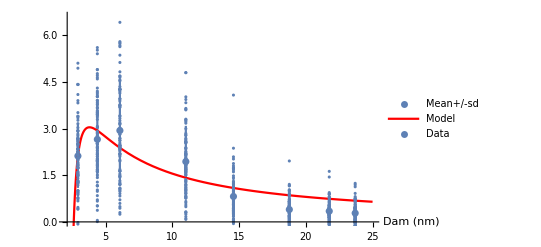

```mathematica
(*Plotting model fit and data*)
plot2=Show[ErrorListPlot[dataplot,AxesLabel->{"Dam (nm)",""},PlotLegends->{"Mean+/-sd"},PlotRange->{{2,25},{0,6.6}},PlotStyle->Grey,PlotRange->All],Plot[nlm[x],{x,2,25},PlotStyle->Red,PlotLegends->{"Model"},PlotRange->All],ListPlot[data,PlotStyle->Grey,PlotLegends->{"Data"},PlotRange->All,AxesLabel->{"Dam (nm)",""}]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

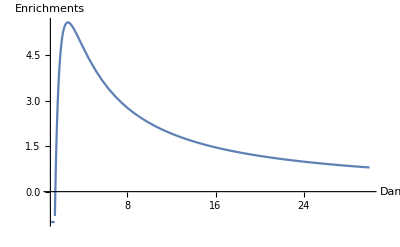

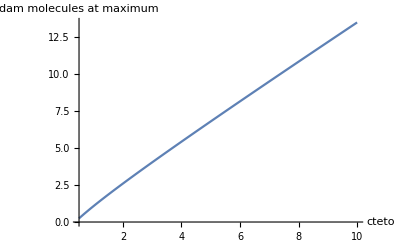

```mathematica
(*Parameter study of the model*)
maximum[i_]:=z/.Flatten[FindMaximum[Enr[z,kd1,kdteto1,kdb1,i,prob1,v1],{z,i}]][[2]]
maxvalue[i_]:=Flatten[FindMaximum[Enr[z,kd1,kdteto1,kdb1,i,prob1,v1],{z,i}]][[1]]
plotkdteto=Plot3D[Enr[x,kd1,y,kdb1,teto1,prob1,v1],{x,0,10},{y,0.1,2.5},AxesLabel->{"Dam","kdteto"},PlotRange->All,PlotLegends->Automatic,ColorFunction->Hue]
plotkdns=Plot3D[Enr[x,y,kdteto1,y,teto1,prob1,v1],{x,1,10},{y,0,200},AxesLabel->{"Dam","kdns"},PlotRange->All,ColorFunction->Hue,PlotLegends->Automatic]
plotconc=Plot3D[Enr[x,kd1,kdteto1,kd1,y,prob1,v1],{x,0.5,10},{y,0.5,10},AxesLabel->{"Dam","teto"},PlotRange->All,PlotLegends->Automatic,ColorFunction->Hue]
Plot[Enr[x,25,0.6,25,teto1,1,v1],{x,1,30},AxesLabel->{"Dam","Enrichments"},PlotRange->All]
Plot[maximum[x],{x,0.5,10},AxesLabel->{"cteto","dam molecules at maximum"}]
```